# Visualization

### Simulation results

The Toolbox provides a series of specialized visualization capabilities that extend Mathematica's own ... of plotting functions.

Plot[stuff] | plot time-profile of simulation
plotPhasePortrait[simulation] | plot a phase-portrait of simulation

Toolbox plotting functions

```mathematica
Needs["Toolbox`Style`"]
Needs["Toolbox`"]
```

```mathematica
model=ExampleData[{"Toolbox","Glycolysis"}];
updateInitialConditions[model,{atp^c->1.1*(atp^c/.model["InitialConditions"])}]
```

```mathematica
{concSol,fluxSol}=simulate[model,{t,0,1000}];
```

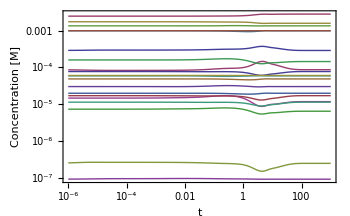

```mathematica
plotSimulation[concSol,FrameLabel->{"t","Concentration [M]"}]
```

### Pathway and network visualization